```mathematica
f[x_]:=x^4-2.3 x^3+0.33 x^2+2.299x-1.331
```

```mathematica
Solve[f[x]==0,x]//N
```

{{x→-1.},{x→1.1},{x→1.1},{x→1.1}}

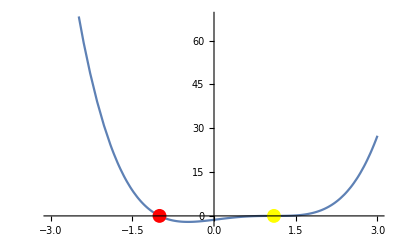

```mathematica
Show[{Plot[f[x],{x,-3,3}],Graphics[{AbsolutePointSize[10],Red,Point[{-1,f[-1]}],Yellow,
Point[{1.0999999999999999,f[1.0999999999999999]}],Purple,AbsolutePointSize[5]
}]
}]
```

```mathematica
Kant[x0_]:={
K=Abs@D[f[x],{x,2}]/.{x->x0};
B=Abs@(1/(D[f[x],x]/.{x-> x0}));
η=Abs@(f[x0]/(D[f[x],x]/.{x-> x0}))//N;
K B η
}//First
```

```mathematica
Kant[{-1-0.1,1.0999999999999999-0.1}]
```

{0.2208,0.654984}

```mathematica
x0=-1.1;
```

```mathematica
fun[x0_]:={
list={x0};
x1=x0-f[x0]/(D[f[x],x]/.{x-> x0});
list=Append[list,x1];
While[Abs[list⟦-1⟧-list[[-2]]]>1/2 10^-5,
xn=list[[-1]]-f[list⟦-1⟧]/(D[f[x],x]/.x->list[[-1]]);
list=Append[list,xn]

];
list
}//First
```

Exact solution x=-1

```mathematica
fun[-1.1]
```

{-1.1,-1.012,-1.0002,-1.,-1.}

```mathematica
Length@fun[0.9]
```

26

```mathematica
1.0999999999999999-0.7
```

0.4

Exact solution x=1.0999999999999999

```mathematica
fun2[x0_]:={
list={x0};
x1=x0-(3f[x0])/(D[f[x],x]/.{x-> x0});
list=Append[list,x1];
While[Abs[list⟦-1⟧-list[[-2]]]>1/2 10^-5,
xn=list[[-1]]-(3f[list⟦-1⟧])/(D[f[x],x]/.x->list[[-1]]);
list=Append[list,xn]

];
list
}//First
```

```mathematica
fun2[0.3999999999999999]
```

{0.4,1.24,1.10286,1.1,1.09987,1.1,-0.4,8.6,2.64959,1.29212,1.10522,1.1,1.09999,1.1,1.09952,1.1,1.1}

```mathematica
Length@fun2[0.3]
```

7